```mathematica
a = Import["C:\\Projects\\CUDA\\vortex\\release\\Kadr02500.txt","Table"];
m = Length[a];
a = Table[a[[i]],{i,2,m}];
m=Length[a]
Sum[a[[i,8]],{i,m-999,m}];
```

9403

```mathematica
Sum[a[[i,8]],{i,1, m}]
```

-2.72327×10^-7

```mathematica
b = Table[a[[i]],{i,m-99,m}];
```

```mathematica
b[[100]]
```

{227,0.008,0.499013,-0.0313953,0.,0.,0.,0.000102406}

```mathematica
a;
```

```mathematica
L=Import["C:\\Projects\\CUDA\\vortex\\vortex\\L","Table"];
birth = Length[L]-1
```

11

```mathematica
M = Import["C:\\Projects\\CUDA\\vortex\\vortex\\m","Table"];
M = Table[M[[i,j]],{i,1,birth+1},{j,1,birth+1}];
```

```mathematica
Table[(L.M)[[i,i]],{i,1,birth+1}];
```

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot :: rect will be suppressed during this calculation.

Part::partw: Part 3 of {« 1 »} . {{-0.0399967, -0.0133235, -0.00798354, -0.00569124, -0.0044148, -0.0036001, -0.00303404, -0.00261714, -0.00229675, -0.00204238, -0.00183517, -0.0016628}, « 10 », {0.00183517, 0.00204238, 0.00229675, 0.00261714, 0.00303404, 0.0036001, 0.0044148, 0.00569124, 0.00798354, 0.0133235, 0.0399967, -0.0399967}} does not exist.

Part::partw: Part 4 of {« 1 »} . {{-0.0399967, -0.0133235, -0.00798354, -0.00569124, -0.0044148, -0.0036001, -0.00303404, -0.00261714, -0.00229675, -0.00204238, -0.00183517, -0.0016628}, « 10 », {0.00183517, 0.00204238, 0.00229675, 0.00261714, 0.00303404, 0.0036001, 0.0044148, 0.00569124, 0.00798354, 0.0133235, 0.0399967, -0.0399967}} does not exist.

Part::partw: Part 5 of {« 1 »} . {{-0.0399967, -0.0133235, -0.00798354, -0.00569124, -0.0044148, -0.0036001, -0.00303404, -0.00261714, -0.00229675, -0.00204238, -0.00183517, -0.0016628}, « 10 », {0.00183517, 0.00204238, 0.00229675, 0.00261714, 0.00303404, 0.0036001, 0.0044148, 0.00569124, 0.00798354, 0.0133235, 0.0399967, -0.0399967}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
Length[L];
```

```mathematica
M//MatrixForm;
```

```mathematica
f = Import["C:\\Projects\\CUDA\\vortex\\F_p.txt","Table"];
```

```mathematica
cx = Table[{f[[i,1]],f[[i,2]]},{i,100,Length[f]}];
```

```mathematica
cx[[1]]
```

{0,0}

```mathematica
ll=120;
cxa =Table[{cx[[i,1]],Sum[cx[[j,2]],{j,i-ll,i+ll}]/(2 ll)},{i,ll+1,Length[cx]-1-ll}];
```

```mathematica
cxaa =ParallelTable[{cxa[[i,1]],Sum[cxa[[j,2]],{j,i-ll,i+ll}]/(2 ll)},{i,ll+1,Length[cxa]-1-ll}];
```

```mathematica
cxaaa =ParallelTable[{cxaa[[i,1]],Sum[cxaa[[j,2]],{j,i-ll,i+ll}]/(2 ll)},{i,ll+1,Length[cxaa]-1-ll}];
```

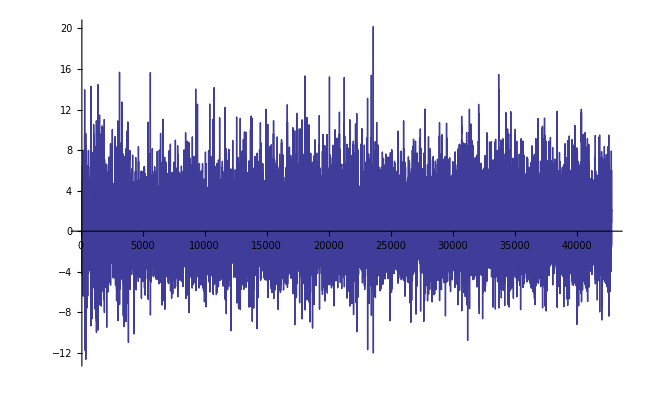

```mathematica
ListLinePlot[cx, PlotRange->All]
```

```mathematica
cy = Table[{f[[i,1]],f[[i,3]]},{i,1,Length[f]}];
cya = Table[{cy[[i,1]],Sum[cy[[j,2]],{j,i,i+100}]/100},{i,1,Length[cy]-101}];
```

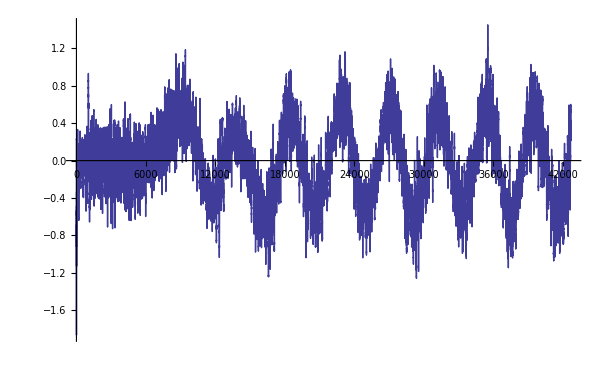

```mathematica
ListLinePlot[cya]
```

```mathematica
mm = Table[{f[[i,1]],f[[i,4]]},{i,1,Length[f]}];
ma = Table[{mm[[i,1]],Sum[mm[[j,2]],{j,i,i+100}]/100},{i,1,Length[mm]-101}];
```

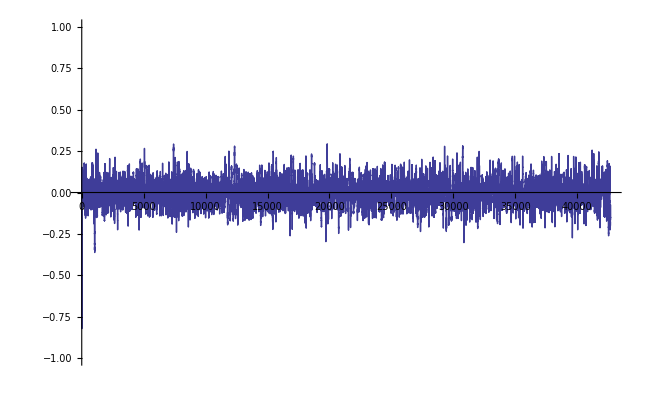

```mathematica
ListLinePlot[ma,PlotRange->{-1,1}]
```